```mathematica
l=0.5;h=6.;m=1.;g=10.;d=0.8;α=1.5;
```

```mathematica
I1=1/3 m (h^2+l^2);I2=1/3 α^5 m (h^2+l^2);J=-1/2 m(d+α l)(d-l/h √(h^2-d^2));
```

```mathematica
NSolve[{(I1 +J)w1==(I1+J) wpr1+I2 wpr2,(I1 +0) w1^2==(I1 +0) wpr1^2+I2 wpr2^2},{wpr1,wpr2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{wpr1→-0.775262 w1,wpr2→0.229214 w1},{wpr1→w1,wpr2→0.}}

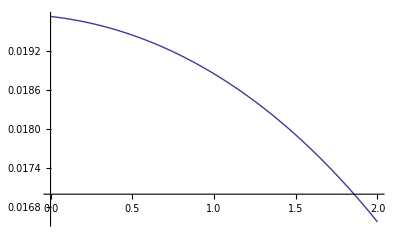

```mathematica
Plot[(2 (I1+ J ))/(I1^2+I1 I2+2 I1 J+J^2)/.α->1.5,{d,0,2}]
```

```mathematica
Solve[{(I1 +J)w1==(I1+J) wpr1+I2 wpr2,(I1 +0) w1^2==(I1 +0) wpr1^2+I2 wpr2^2},{wpr1,wpr2}]
```

{{wpr1→w1,wpr2→0},{wpr1→(I1^2 w1-I1 I2 w1+2 I1 J w1+J^2 w1)/(I1^2+I1 I2+2 I1 J+J^2),wpr2→(2 (I1^2 w1+I1 J w1))/(I1^2+I1 I2+2 I1 J+J^2)}}

```mathematica
resu=(2 (I1^2 w1+I1 J w1))/(I1^2+I1 I2+2 I1 J+J^2)
```

(2 (I1^2 w1+I1 J w1))/(I1^2+I1 I2+2 I1 J+J^2)

```mathematica
Solve[I1 w1^2==m g (√(h^2+l^2)-√(h^2-d^2)-(l d)/h),w1]
```

{{w1→-(√(-g √(-d^2+h^2) m-(d g l m)/h+g √(h^2+l^2) m))/(√I1)},{w1→(√(-g √(-d^2+h^2) m-(d g l m)/h+g √(h^2+l^2) m))/(√I1)}}

```mathematica
l=1.;h=6.;m=1.;g=10.;
```

```mathematica
sol=resu/.w1->0.1+(√3 √(-g √(-d^2+h^2)-(d g l)/h+g √(h^2+l^2)))/(√(3 d^2+h^2+l^2+6 d l α+3 l^2 α^2))
```

(2 (152.111 (0.1+(√3 √(60.8276-1.66667 d-10. √(36.-d^2)))/(√(37.+3 d^2+6. d α+3. α^2)))-6.16667 (d-0.166667 √(36.-d^2)) (d+1. α) (0.1+(√3 √(60.8276-1.66667 d-10. √(36.-d^2)))/(√(37.+3 d^2+6. d α+3. α^2)))))/(152.111+152.111 α^5-12.3333 (d-0.166667 √(36.-d^2)) (d+1. α)+0.25 (d-0.166667 √(36.-d^2))^2 (d+1. α)^2)

```mathematica
sol1=I2 sol^2-m  g α^5(√(h^2+l^2)-h)
```

-0.827625 α^5+(49.3333 α^5 (152.111 (0.1+(√3 √(60.8276-1.66667 d-10. √(36.-d^2)))/(√(37.+3 d^2+6. d α+3. α^2)))-6.16667 (d-0.166667 √(36.-d^2)) (d+1. α) (0.1+(√3 √(60.8276-1.66667 d-10. √(36.-d^2)))/(√(37.+3 d^2+6. d α+3. α^2))))^2)/((152.111+152.111 α^5-12.3333 (d-0.166667 √(36.-d^2)) (d+1. α)+0.25 (d-0.166667 √(36.-d^2))^2 (d+1. α)^2)^2)

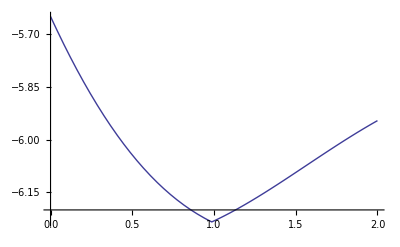

```mathematica
Plot[sol1/.α->1.5,{d,0,2}]
```

```mathematica
m g (√(h^2+l^2)-√(h^2-d^2)-(l d)/h)/.d->1
```

0.000160805

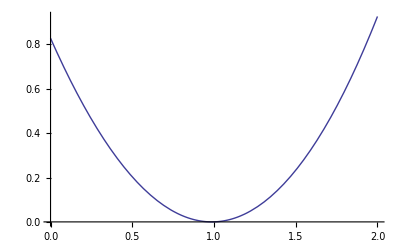

```mathematica
Plot[m g (√(h^2+l^2)-√(h^2-d^2)-(l d)/h),{d,0,2}]
```

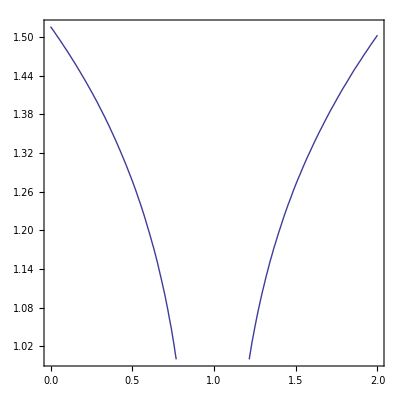

```mathematica
ContourPlot[sol==0.051,{d,0,2},{α,1,2},PlotRange->All]
```

```mathematica
NSolve[(sol/.α->1.5)==0,d]
```

{{d→-1.64733+5.85342 ⅈ},{d→-1.64733-5.85342 ⅈ},{d→-1.45392+5.45448 ⅈ},{d→-1.45392-5.45448 ⅈ}}